(16.03.2021) Определение погрешности измерений крит. экспонент в коллапсе данных для квадрата теплоёмкости

```mathematica
newData=Import["https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Canonical_near_phase/all.txt", "Table"];
```

Возьмём длины 100-1000

https://raw.githubusercontent.com/kamilla0503/saw/master/Ising/Canonical_near_phase/all.txt

```mathematica
allData={};
Ls={500,600,750,1000};
Do[
AppendTo[allData,Select[newData,#[[1]]==L&][[All,{1,2,16}]]];
,{L,Ls}]
```

Стоит отметить, что в формулах фигурируют не длины систем, а их квадратные корни (так как N = L * L, где L - используемая в формулах величина)

Воспользуемся рассчитанными ранее значениями экспонент (b = 1/8, ν = 1) и определим погрешность для крит. температуры.

```mathematica
Tc0=1.1976;
v0 = 1;
b0 = 1/8;
Ls0 = Ls ст
```

{500 ст,600 ст,750 ст,1000 ст}

```mathematica
Manipulate[ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->JoinQ, Mesh->DotsQ, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}],{Tc,1.19,1.20,0.001}, {JoinQ,{True,False}},{DotsQ,{False,All}}]
```

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

Part::partw: Part 2 of #1 does not exist.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$17) (#1⟦1⟧)^(0.5 v0),#1⟦3⟧ (#1⟦1⟧)^(b0/v0)}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MapAt::partw: Part {All,All} of allData does not exist.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$17) (#1⟦1⟧)^(0.5 v0),#1⟦3⟧ (#1⟦1⟧)^(b0/v0)}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$17) (#1⟦1⟧)^(0.5 v0),#1⟦3⟧ (#1⟦1⟧)^(b0/v0)}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MapAt::partw: Part {All,All} of allData does not exist.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$17) (#1⟦1⟧)^(0.5 v0),#1⟦3⟧ (#1⟦1⟧)^(b0/v0)}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

MapAt::partw: Part {All,All} of allData does not exist.

General::stop: Further output of MapAt::partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[{(1./Part[«2»]-1. FE`Tc$$17) (#1⟦1⟧)^(0.5 v0),#1⟦3⟧ (#1⟦1⟧)^(b0/v0)}&,allData,{All,All}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Наилучший коллапс данных виден между 1.19 и 1.20, поэтому итоговое значение Tc - 1.195 ± 0.005

```mathematica
Manipulate[ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v),#[[3]]*(#[[1]])^(b/v)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, {0,2.5}}, Joined->JoinQ, Mesh->DotsQ, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}],{v,0.95,1.05,0.01},{b,0.11,0.13,0.001},{Tc,1.19,1.20,0.001}, {JoinQ,{True,False}},{DotsQ,{False,All}}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 500^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 500^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 500^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ν = 1±0.05
b = 0.12±0.1
```

Графики сравнения (Критическая температура):

```mathematica
Tc0=1.19;
v0 = 1;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc0)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[1], ImageSize->700];
Tc1=1.2;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc1)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[10], ImageSize->700];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

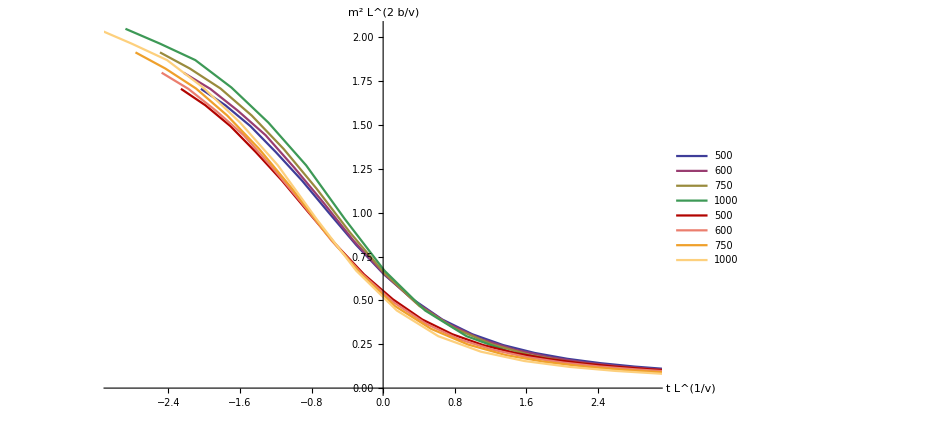

```mathematica
Tc0=1.19;
v0 = 1;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc0)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700, PlotMarkers->{"●", 8}];
Tc1=1.2;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc1)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700,PlotMarkers->{"●", 8}];
Show[PlTempLeft,PlTempRight,AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

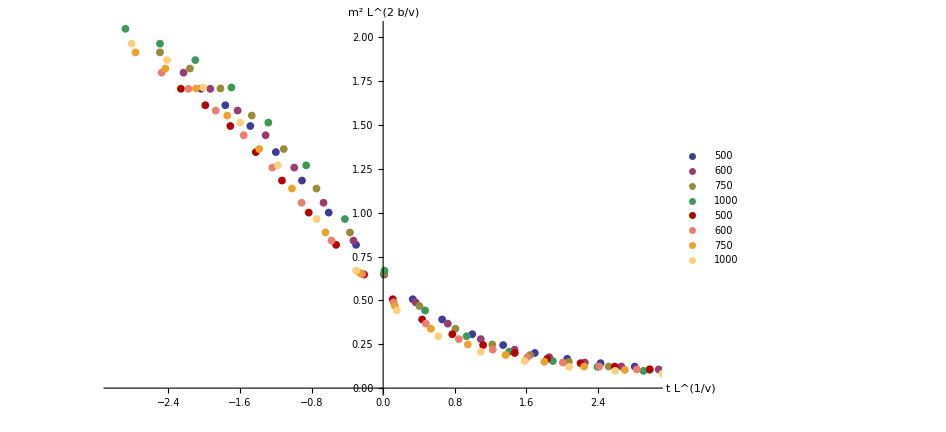

```mathematica
Tc0=1.19;
v0 = 1;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc0)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700,PlotMarkers->{▼,10}];
Tc1=1.2;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc1)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700, PlotMarkers->{●,10}];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

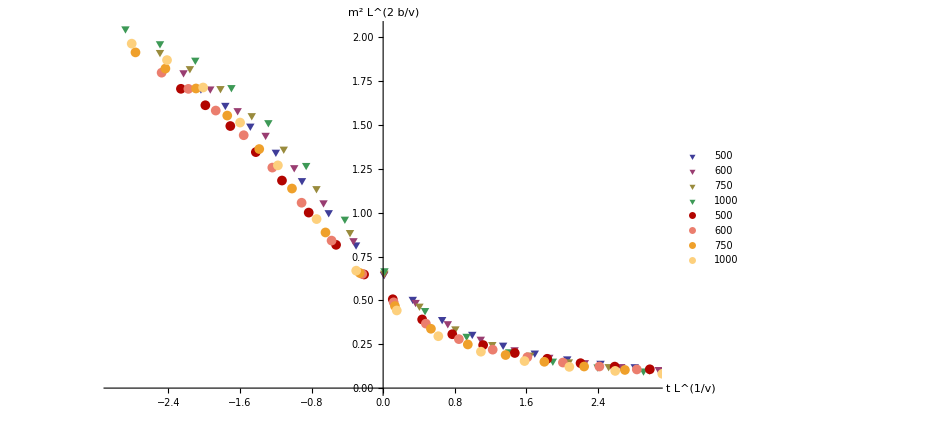

Графики сравнения (экспонента ν):

```mathematica
Tc=1.195;
v0 = 0.95;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[1], ImageSize->700];
v1=1.05;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v1),#[[3]]*(#[[1]])^(b0/v1)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[10], ImageSize->700];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

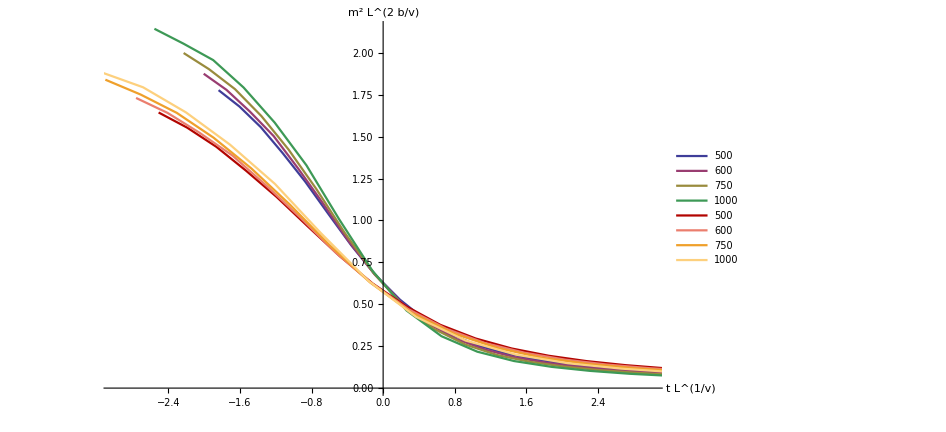

```mathematica
Tc=1.195;
v0 = 0.95;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700, PlotMarkers->{"●", 8}];
v1=1.05;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v1),#[[3]]*(#[[1]])^(b0/v1)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700, PlotMarkers->{"●", 8}];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

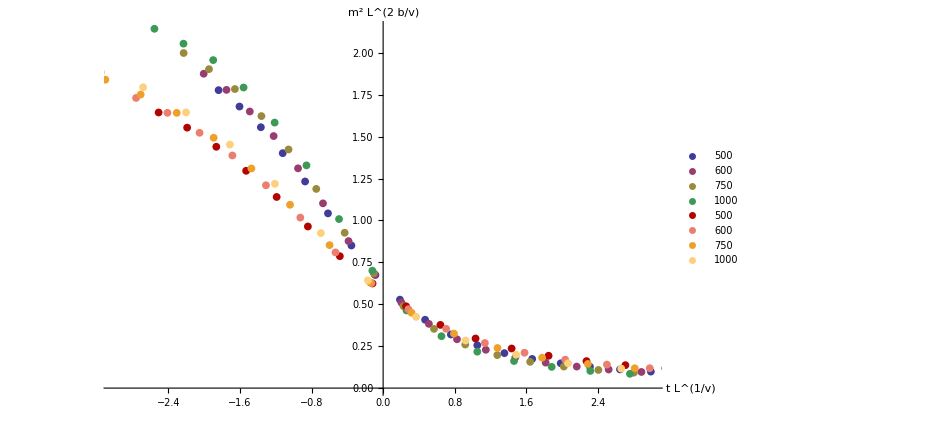

```mathematica
Tc=1.195;
v0 = 0.95;
b0 = 1/8;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700, PlotMarkers->{▼,8}];
v1=1.05;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v1),#[[3]]*(#[[1]])^(b0/v1)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700, PlotMarkers->{●, 8}];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

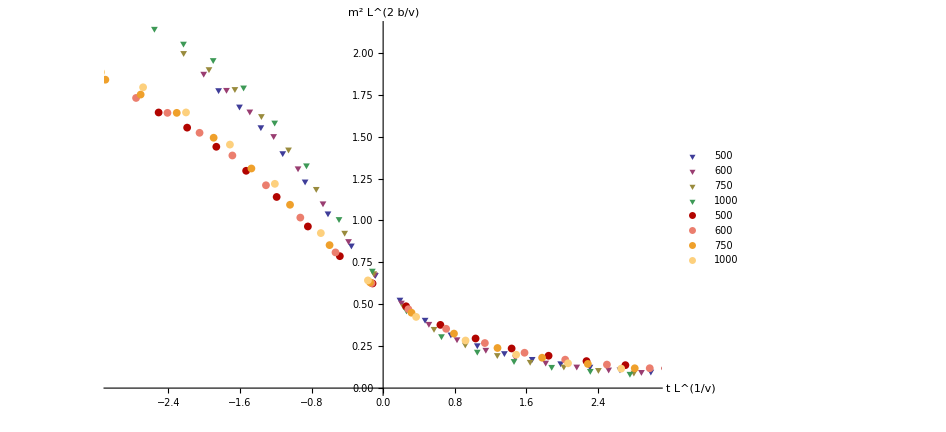

Графики сравнения (экспонента β):

```mathematica
Tc=1.195;
v0 = 1;
b0 = 0.12;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[1], ImageSize->700];
b1=0.13;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b1/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, Joined->True, PlotStyle->ColorData[10], ImageSize->700];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

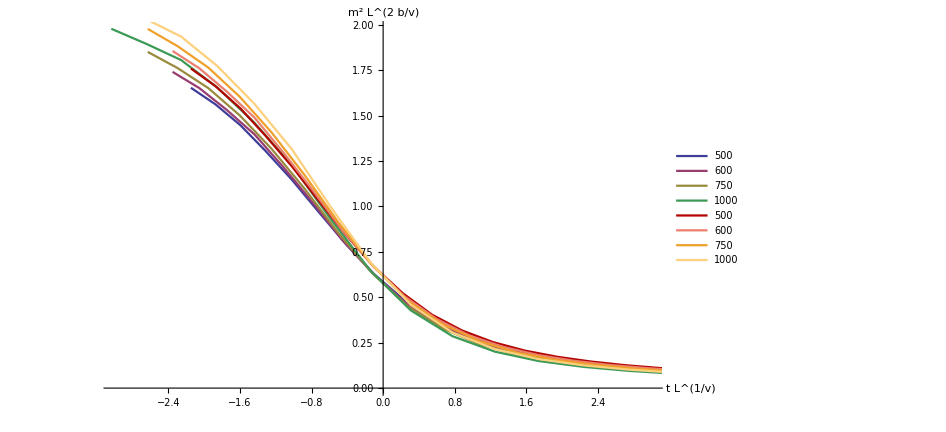

```mathematica
Tc=1.195;
v0 = 1;
b0 = 0.12;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700, PlotMarkers->{"●", 8}];
b1=0.13;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b1/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700, PlotMarkers->{"●", 8}];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```

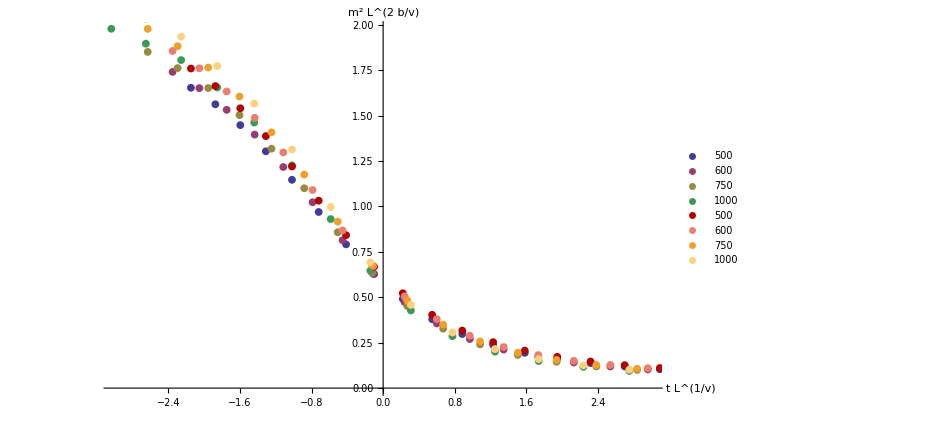

```mathematica
Tc=1.195;
v0 = 1;
b0 = 0.12;
PlTempLeft=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b0/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[1], ImageSize->700, PlotMarkers->{▼, 8}];
b1=0.13;
PlTempRight=ListPlot[MapAt[{(1/#[[2]]-Tc)*(#[[1]])^(1/2v0),#[[3]]*(#[[1]])^(b1/v0)}&,allData,{All,All}],PlotLegends->Ls,PlotRange->{{-3,3}, All}, PlotStyle->ColorData[10], ImageSize->700, PlotMarkers->{●, 8}];
Show[PlTempLeft,PlTempRight, AxesLabel->{"t L^(1/v)", "m^2 L^(2  b/v)"}]
```